# Ordinary differential equations and related problems

## Auxiliary built-in functions

It is straightforward to get series expansion of a given function in a neighborhood of a given point. This is useful in linearisation/approximation of non-linear equations.

```mathematica
Series[Sin[x] - Cos[x],{x,0,10}]
SeriesCoefficient[%, 3]
```

-1+x+x^2/2-x^3/6-x^4/24+x^5/120+x^6/720-x^7/5040-x^8/40320+x^9/362880+x^10/3628800+O[x]^11

-1/6

Symbolic manipulations with trigonometric functions are possible. Think of Fourier series!  We need product-to-sum conversions and so forth.

```mathematica
Sin[x] + Sin[y]
TrigFactor[Sin[x] + Sin[y]] (* sister commands are TrigReduce, TrigExpand, TrigFactor *)
```

Sin[x]+Sin[y]

2 Cos[x/2-y/2] Sin[x/2+y/2]

```mathematica
TrigReduce[%]
```

Sin[x]+Sin[y]

This is probably a better readable form .

```mathematica
(Sin[2*x])^3 + Sin[x] ==TrigReduce[(Sin[2*x])^3 + Sin[x]] // TraditionalForm
```

sin^3(2 x)+sin(x)==1/4 (4 sin(x)+3 sin(2 x)-sin(6 x))

It is straightforward to get the coefficients.

```mathematica
Coefficient[TrigReduce[(Sin[2*x])^3 + Sin[x]] , Sin[2*x]] (* get one of the coefficients in fundamental harmonics *)
```

3/4

We can solve algebraic as well as differential equations (symbolic solvers). Note the data structure used for reporting the solution.

```mathematica
Solve[x^2+5*x+6 == 0, x]
```

{{x→-3},{x→-2}}

## Ordinary differential equations

### Preliminaries

First we need to know how to differentiate a function.

```mathematica
D[x^2, x]
```

2 x

The pattern based programming allows us to easily supply the function as an input to a different function. (In my old programming days in C this construction used the concept of “pointer to a function”.)

```mathematica
myRescaledDerivative[fn_[s_, u___], n_]:= D[fn[s/n, u], s]
```

```mathematica
myRescaledDerivative[y[x], n]
```

y'[x/n]/n

```mathematica
myRescaledDerivative[Power[x,2], n]
```

(2 x)/n^2

### Symbolic solution

But let us go back to our original goal. We want to solve differential equations. First we try to solve one symbolically.

```mathematica
DSolve[y''[t] + 3*y'[t] + 8* y[t] == 0, y, t]
DSolve[y''[t] + 3*y'[t] + 8* y[t] == 0, y[t], t] (* Note the difference between outputs. *)
```

{{y→Function[{t},ⅇ^(-3 t/2) C[2] Cos[(√23 t)/2]+ⅇ^(-3 t/2) C[1] Sin[(√23 t)/2]]}}

{{y[t]→ⅇ^(-3 t/2) C[2] Cos[(√23 t)/2]+ⅇ^(-3 t/2) C[1] Sin[(√23 t)/2]}}

Let us store the result, and let us see what can be done with the result.

```mathematica
odeSol = DSolve[y''[t] + 3*y'[t] + 8* y[t] == 0, y, t]
```

{{y→Function[{t},ⅇ^(-3 t/2) C[2] Cos[(√23 t)/2]+ⅇ^(-3 t/2) C[1] Sin[(√23 t)/2]]}}

We want  to find the derivative of the solution  or for that matter evaluate any expression involving the solution.

```mathematica
y'[t] + (y[t])^2 /. odeSol
```

{1/2 √23 ⅇ^(-3 t/2) C[1] Cos[(√23 t)/2]-3/2 ⅇ^(-3 t/2) C[2] Cos[(√23 t)/2]-3/2 ⅇ^(-3 t/2) C[1] Sin[(√23 t)/2]-1/2 √23 ⅇ^(-3 t/2) C[2] Sin[(√23 t)/2]+(ⅇ^(-3 t/2) C[2] Cos[(√23 t)/2]+ⅇ^(-3 t/2) C[1] Sin[(√23 t)/2])^2}

Let us solve a boundary value problem  and plot the solution. We can in fact plot any function of the solution.

{{y→Function[{t},(2 ⅇ^(-3 t/2) Sin[(√23 t)/2])/(√23)]}}

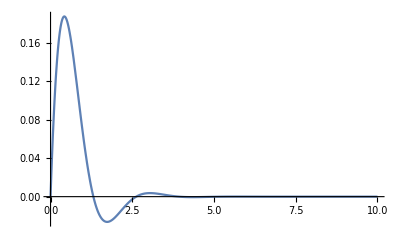

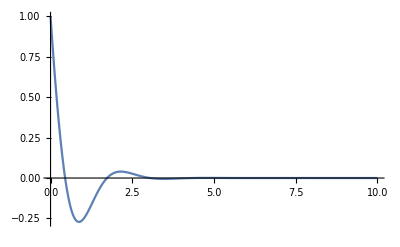

```mathematica
odeSolIC = DSolve[{y''[t] + 3*y'[t] + 8* y[t] == 0, y[0] == 0, y'[0] == 1}, y, t]
Plot[y[t] /. odeSolIC, {t, 0, 10}, PlotRange->All]
Plot[(y'[t] + (y[t])^2 ) /. odeSolIC, {t, 0, 10}, PlotRange->All]
```

### Numerical solution

Most of ordinary differential equations do not have an analytical solution . But usually we know that the solution exists and it is unique. The solution can be found  numerically. The result is the INTERPOLATING function (polynomial interpolant of the calculated discrete values). The interpolating function can be used in other operations. BE CAREFUL, if you as for the value of the interpolating function beyond the original interval, you still get a number, bit it is a nonsense. (It is obtained via extrapolation.)

```mathematica
odeSolICNum:= NDSolve[{y''[t] == -y[t], y[0] == 0, y'[0] == 1}, y, {t,0,2*π}]
```

{{y→InterpolatingFunction[…]}}

{0.479426}

{6.00843×10^-8}



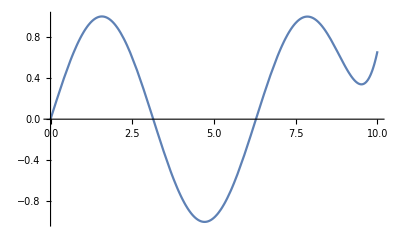

```mathematica
odeSolICNum
y[1/2] /. odeSolICNum
y'[π/2] /. odeSolICNum
Plot[Evaluate[y[t] /. odeSolICNum], {t, 0 ,2*π}]
Plot[Evaluate[y[t] /. odeSolICNum], {t, 0 ,10}] (* Extrapolation from the interval (0,2*pi). DO NOT DO THIS! *)
```

You can use different numerical methods, you can set up different stopping criteria and so forth. Read the manual. Concerning the problems we will be interested in the motion of an pendulum, which is in the undampened case a Hamiltonian system. Integration method “SymplecticPartitionedRungeKutta” might be of interest here. (ProjectionMethod can be forces to do the same.) Another useful construct is the “EvaluationMonitor”. There are many of them! Read the manual.

```mathematica
odeSolICNumEuler:= NDSolve[{y''[t] == -y[t], y[0] == 0, y'[0] == 1}, y, {t,0,2*π}, StartingStepSize->2*π/100, Method->{"TimeIntegration"->"ExplicitEuler"},  StepMonitor:>If[printResults, Print["Step number [", nSteps++,"]: y[t] = ",y[t],", t =",t], {}]]
```

```mathematica
nSteps = 1; 
printResults = True; 
odeSolICNumEuler
```

Step number [1]: y[t] = 0.0628319, t =0.0628319

Step number [2]: y[t] = 0.125664, t =0.125664

Step number [3]: y[t] = 0.188248, t =0.188496

Step number [4]: y[t] = 0.250335, t =0.251327

Step number [5]: y[t] = 0.31168, t =0.314159

Step number [6]: y[t] = 0.372036, t =0.376991

Step number [7]: y[t] = 0.431162, t =0.439823

Step number [8]: y[t] = 0.488819, t =0.502655

Step number [9]: y[t] = 0.544774, t =0.565487

Step number [10]: y[t] = 0.598799, t =0.628319

Step number [11]: y[t] = 0.650673, t =0.69115

Step number [12]: y[t] = 0.700184, t =0.753982

Step number [13]: y[t] = 0.747125, t =0.816814

Step number [14]: y[t] = 0.791303, t =0.879646

Step number [15]: y[t] = 0.832531, t =0.942478

Step number [16]: y[t] = 0.870635, t =1.00531

Step number [17]: y[t] = 0.905452, t =1.06814

Step number [18]: y[t] = 0.936832, t =1.13097

Step number [19]: y[t] = 0.964638, t =1.19381

Step number [20]: y[t] = 0.988745, t =1.25664

Step number [21]: y[t] = 1.00904, t =1.31947

Step number [22]: y[t] = 1.02544, t =1.3823

Step number [23]: y[t] = 1.03785, t =1.44513

Step number [24]: y[t] = 1.04622, t =1.50796

Step number [25]: y[t] = 1.05048, t =1.5708

Step number [26]: y[t] = 1.05062, t =1.63363

Step number [27]: y[t] = 1.04661, t =1.69646

Step number [28]: y[t] = 1.03845, t =1.75929

Step number [29]: y[t] = 1.02616, t =1.82212

Step number [30]: y[t] = 1.00977, t =1.88496

Step number [31]: y[t] = 0.989326, t =1.94779

Step number [32]: y[t] = 0.964898, t =2.01062

Step number [33]: y[t] = 0.936565, t =2.07345

Step number [34]: y[t] = 0.904422, t =2.13628

Step number [35]: y[t] = 0.868582, t =2.19911

Step number [36]: y[t] = 0.829172, t =2.26195

Step number [37]: y[t] = 0.786332, t =2.32478

Step number [38]: y[t] = 0.740219, t =2.38761

Step number [39]: y[t] = 0.691002, t =2.45044

Step number [40]: y[t] = 0.638862, t =2.51327

Step number [41]: y[t] = 0.583995, t =2.57611

Step number [42]: y[t] = 0.526605, t =2.63894

Step number [43]: y[t] = 0.46691, t =2.70177

Step number [44]: y[t] = 0.405135, t =2.7646

Step number [45]: y[t] = 0.341518, t =2.82743

Step number [46]: y[t] = 0.276301, t =2.89027

Step number [47]: y[t] = 0.209736, t =2.9531

Step number [48]: y[t] = 0.14208, t =3.01593

Step number [49]: y[t] = 0.0735962, t =3.07876

Step number [50]: y[t] = 0.00455134, t =3.14159

Step number [51]: y[t] = -0.0647841, t =3.20442

Step number [52]: y[t] = -0.134137, t =3.26726

Step number [53]: y[t] = -0.203235, t =3.33009

Step number [54]: y[t] = -0.271803, t =3.39292

Step number [55]: y[t] = -0.339569, t =3.45575

Step number [56]: y[t] = -0.406261, t =3.51858

Step number [57]: y[t] = -0.471614, t =3.58142

Step number [58]: y[t] = -0.535362, t =3.64425

Step number [59]: y[t] = -0.597248, t =3.70708

Step number [60]: y[t] = -0.657021, t =3.76991

Step number [61]: y[t] = -0.714436, t =3.83274

Step number [62]: y[t] = -0.769257, t =3.89557

Step number [63]: y[t] = -0.821258, t =3.95841

Step number [64]: y[t] = -0.870222, t =4.02124

Step number [65]: y[t] = -0.915943, t =4.08407

Step number [66]: y[t] = -0.95823, t =4.1469

Step number [67]: y[t] = -0.9969, t =4.20973

Step number [68]: y[t] = -1.03179, t =4.27257

Step number [69]: y[t] = -1.06274, t =4.3354

Step number [70]: y[t] = -1.08962, t =4.39823

Step number [71]: y[t] = -1.1123, t =4.46106

Step number [72]: y[t] = -1.13068, t =4.52389

Step number [73]: y[t] = -1.14467, t =4.58673

Step number [74]: y[t] = -1.1542, t =4.64956

Step number [75]: y[t] = -1.1592, t =4.71239

Step number [76]: y[t] = -1.15965, t =4.77522

Step number [77]: y[t] = -1.15553, t =4.83805

Step number [78]: y[t] = -1.14682, t =4.90088

Step number [79]: y[t] = -1.13356, t =4.96372

Step number [80]: y[t] = -1.11577, t =5.02655

Step number [81]: y[t] = -1.0935, t =5.08938

Step number [82]: y[t] = -1.06682, t =5.15221

Step number [83]: y[t] = -1.03583, t =5.21504

Step number [84]: y[t] = -1.00063, t =5.27788

Step number [85]: y[t] = -0.961341, t =5.34071

Step number [86]: y[t] = -0.9181, t =5.40354

Step number [87]: y[t] = -0.871063, t =5.46637

Step number [88]: y[t] = -0.820402, t =5.5292

Step number [89]: y[t] = -0.766302, t =5.59203

Step number [90]: y[t] = -0.708963, t =5.65487

Step number [91]: y[t] = -0.648599, t =5.7177

Step number [92]: y[t] = -0.585436, t =5.78053

Step number [93]: y[t] = -0.519713, t =5.84336

Step number [94]: y[t] = -0.451678, t =5.90619

Step number [95]: y[t] = -0.381592, t =5.96903

Step number [96]: y[t] = -0.309722, t =6.03186

Step number [97]: y[t] = -0.236346, t =6.09469

Step number [98]: y[t] = -0.161747, t =6.15752

Step number [99]: y[t] = -0.0862153, t =6.22035

Step number [100]: y[t] = -0.0100449, t =6.28319

{{y→InterpolatingFunction[…]}}

```mathematica
printResults = False; 
odeSolICNumEuler
```

{{y→InterpolatingFunction[…]}}

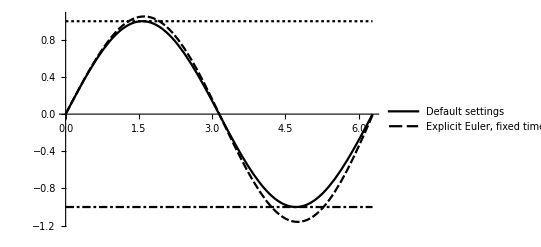

```mathematica
Plot[{Evaluate[y[t] /. odeSolICNum],  Evaluate[y[t] /. odeSolICNumEuler], 1, -1}, {t, 0 ,2*π}, PlotLegends->{"Default settings", "Explicit Euler, fixed time step"}, PlotTheme->"Monochrome"]
```

Very useful construct is WhenEvent. The equation is integrated numerically and when a criterion is met an action is taken. The bouncing example clarifies the use of the WhenEvent construct.

{{y→InterpolatingFunction[…]}}

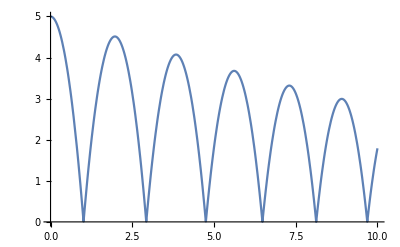

```mathematica
NDSolve[{y''[t]==-9.81,y[0]==5,y'[0]==0,WhenEvent[y[t]==0,y'[t]->-0.95y'[t]]},y,{t,0,10}]
Plot[y[t]/.%,{t,0,10}]
```

The second order differential equation can be turned into a system of first order differential equations (position, velocity). We can plot the corresponding vector field.

{{y[t]→InterpolatingFunction[…][t],v[t]→InterpolatingFunction[…][t]}}

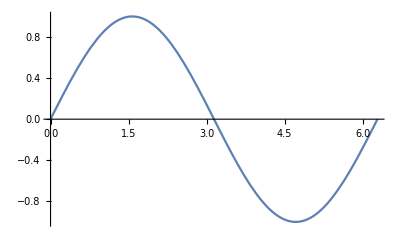

```mathematica
odeSolSys := NDSolve[{v'[t] ==  -y[t], y'[t] == v[t], y[0] == 0, v [0] == 1}, {y[t], v [t]}, {t, 0, 2*π}]
odeSolSys
Plot[Evaluate[y[t] /. odeSolSys], {t, 0, 2*π}]
```

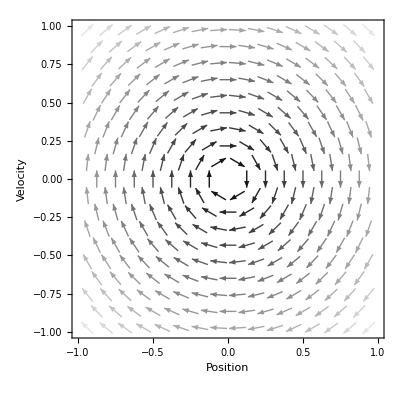

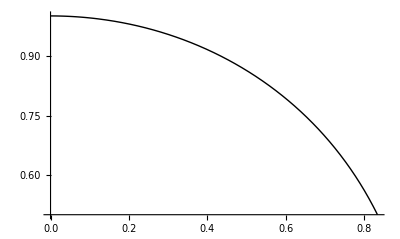

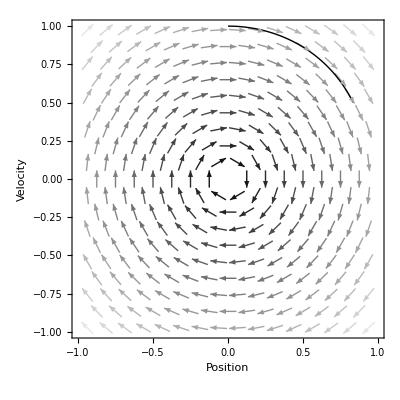

```mathematica
vField := VectorPlot[{v, -y}, {y, -1,1}, {v,-1,1}, PlotTheme->"Monochrome", FrameLabel->{"Position", "Velocity"}]
vField
odeTrajectory:= ParametricPlot[Evaluate[{y[t], v[t]} /. odeSolSys], {t, 0, 1}, PlotTheme->"Monochrome", PlotStyle->Thick]
odeTrajectory
Show[{vField, odeTrajectory}]
```

We can make a fancy version of the same .

```mathematica
Manipulate[
vField := VectorPlot[{v, -y}, {y, -1,1}, {v,-1,1}, PlotTheme->"Monochrome", FrameLabel->{"Position", "Velocity"}, AspectRatio->1];
odeSolSys := NDSolve[{v'[t] ==  -y[t], y'[t] == v[t], y[0] == icPoint[[1]], v [0] == icPoint[[2]]}, {y[t], v [t]}, {t, 0, tMax}];
odeTrajectory:= ParametricPlot[Evaluate[{y[t], v[t]} /. odeSolSys], {t, 0, tMax}, PlotTheme->"Monochrome", PlotStyle->Thick];
Show[{vField, odeTrajectory}, ImageSize->Large]
,
{tMax, 1/100, 2*π},
{{icPoint,{0,1}},Locator},
SaveDefinitions->True
]
```

We will often encounter the problem of plotting the solution to an ordinary differential equation for a range of parameters. There is a canonical way how to do it. (Check also ParametricNDSolveValue.)

{y→ParametricFunction[<>]}

{y→ParametricFunction[<>]}

1.64872

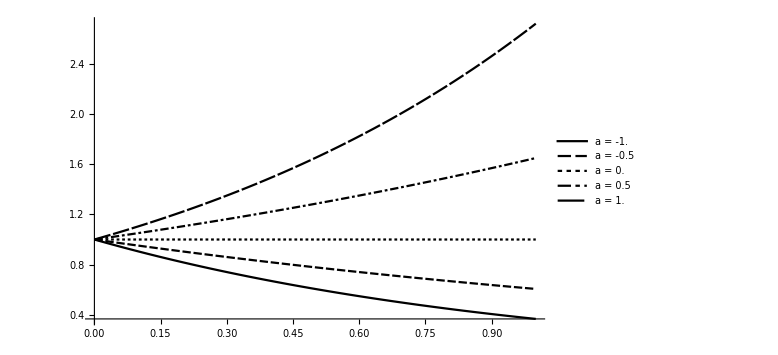

```mathematica
odeSolParam = ParametricNDSolve[{y'[t]==a y[t],y[0]==1},y,{t,0,1},{a}]
odeSolParam

y[1][1/2] /. odeSolParam (* y[a, t] the function has now two arguments -- parameter value and time *)

Plot[Evaluate[Table[y[a][t]/.odeSolParam,{a,-1,1,0.5}]],{t,0,1},PlotRange->All, PlotLegends->Table["a = " <> ToString[a], {a,-1,1,0.5}], PlotTheme->"Monochrome", ImageSize->Large]
```